```mathematica
lst=Table[0,8,61];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->10};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"733.4204841489715`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"1463.1378463776634`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"708.973134677339`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"General\", \"::\", \"munfl\"}], \"MessageName\"]\) will be suppressed during this calculation."
```

```mathematica
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},Joined->True]]
```

-Graphics-

```mathematica
Export["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_ana.dat",lst]
corr0=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_0.dat",Number];
corr1=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_1.dat",Number];
corr2=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_2.dat",Number];
corr3=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_3.dat",Number];
corr4=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_4.dat",Number];
corr5=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_5.dat",Number];
corr6=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_6.dat",Number];
corr7=ReadList["F:\\ThesisProject\\RESULTS\\22052023_corr_ana_h10\\corr_s_7.dat",Number];
```

F:\ThesisProject\RESULTS\22052023_corr_ana_h10\corr_ana.dat

```mathematica
plst=Table[0,{i,8},{j,31},{k,2}];
For[i=0,i<8,i++,plst[[i+1]]=Transpose[{Table[i,{i,-30,30}],lst[[i+1]]}]];
```

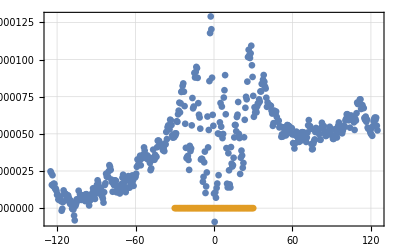

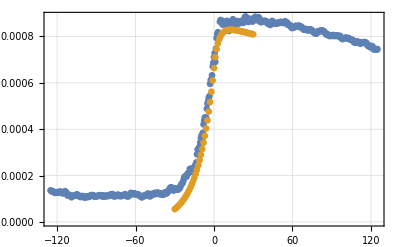

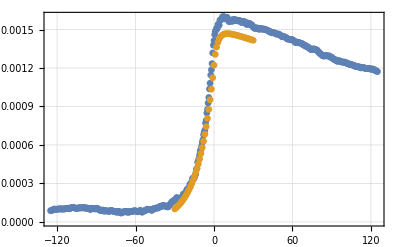

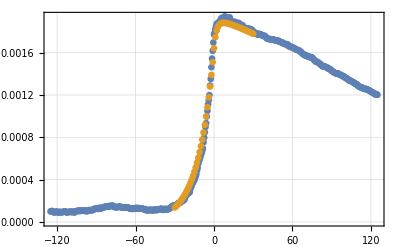

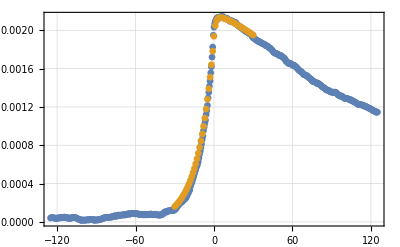

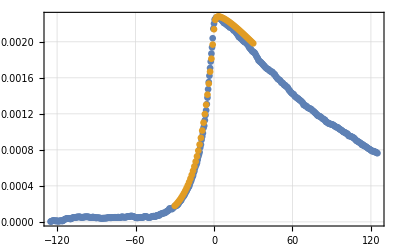

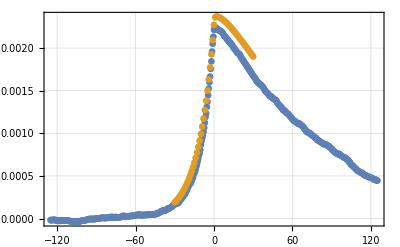

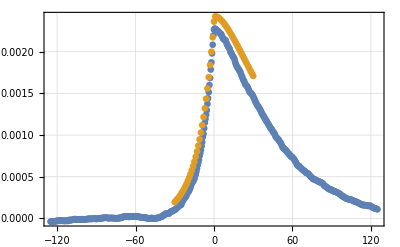

```mathematica
scalF=10;
pcr0=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr0}];

ListPlot[{pcr0,plst[[1]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr1=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr1}];

ListPlot[{pcr1,plst[[2]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr2=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr2}];

ListPlot[{pcr2,plst[[3]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr3=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr3}];

ListPlot[{pcr3,plst[[4]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr4=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr4}];

ListPlot[{pcr4,plst[[5]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr5=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr5}];

ListPlot[{pcr5,plst[[6]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr6=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr6}];

ListPlot[{pcr6,plst[[7]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr7=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr7}];

ListPlot[{pcr7,plst[[8]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
```

```mathematica
(**)
```

```mathematica
lst=Table[0,8,31];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fDCtau[i],{i,0,30}]];
```

General::munfl: 8.59599×10^-302 1.48915×10^-16 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.565] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-737.136] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{0,30},Joined->True]]
```

-Graphics-

```mathematica
(**)
```

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
fCtauP[t]
```

-1.+((2. (1))/((1) (1.+4+(1 1)/(2.+3+1)))+1/1+38+2.71828^(2.71828^1 t 1) (1))/(((2. (1))/1+(4. (1))/1+1/1+1/1+(2. (1))/1+(2. (1))/1) (1/1+4+1/1))
 |  |  |  |

```mathematica
Maximize[Out[30],t∈Interval[{0,7}]]
```

Maximize::objfs: The objective function {<<3147959160 bytes>>} should be scalar-valued.

Maximize[-1.+((2. (1))/((1) (1.+4+(1 1)/(2.+3+1)))+39+2.71828^(18^1 111) (1))/(((2. (1))/1+(4. (1))/1+1/1+1/1+(2. (1))/1+(2. (1))/1) (1)),t∈Interval[{0,7}]]
 |  |  |  |

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->5,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
fCtauP[t]
```

-1.+0.140648 (7.10997-9.0886×10^-6 2.71828^(-82.1121 t)+1.03161×10^-7 2.71828^(-11.6856 t)-0.00481026 2.71828^(-2.45446 t)-0.0491367 2.71828^(-0.181643 t)+0.120051 2.71828^(-0.0740875 t))

```mathematica
Maximize[%,t]
```

{0.0098589,{t→1.06526}}

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->1,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
fCtauP[t]
Maximize[%,t]
```

-1.+0.166347 (6.01152-0.0000225717 2.71828^(-24.5712 t)+8.84665×10^-9 2.71828^(-11.6856 t)-0.00462064 2.71828^(-0.658387 t)-0.00283983 2.71828^(-0.181643 t)+0.02463 2.71828^(-0.019472 t))

{0.00350677,{t→4.1399}}

```mathematica
Out[43][[1]]
```

0.00350677

```mathematica
Out[43][[2]]
```

{t→4.1399}

```mathematica
t/.t->Out[43][[2,1,2]]
```

4.1399

```mathematica
lst
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
lst[[1]]
```

{0,0}

```mathematica
lst
```

{{1.59073×10^-12,-0.519566},{0.00625079,3.3005},{0.0091827,1.62697},{0.0102691,0.679211},{0.0106702,0.263381},{0.0108184,0.0989795}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt",lst]
```

F:\ThesisProject\RESULTS\24052023_extrema\h7.txt

```mathematica
lst
```

{{-1.+0.167507 (5.96988+1.39436×10^-16 2.71828^(-48.7713 t)-1.84314×10^-18 2.71828^(-24.4473 t)+2.23446×10^-16 2.71828^(-0.287372 t)-9.82599×10^-10 2.71828^(-0.0829146 t)-2.00492×10^-15 2.71828^(-0.00189419 t)),Maximize[-1.+0.167507 (5.96988+1.39436×10^-16 2.71828^(-48.7713 t)-1.84314×10^-18 2.71828^(-24.4473 t)+2.23446×10^-16 2.71828^(-0.287372 t)-9.82599×10^-10 2.71828^(-0.0829146 t)-2.00492×10^-15 2.71828^(-0.00189419 t)),t∈Interval[{-10,10}]]⟦2,1,2⟧},{-1.+0.155264 (6.44064-1.7059×10^-6 2.71828^(-61.9946 t)+1.1957×10^-11 2.71828^(-24.4473 t)-0.0016861 2.71828^(-0.385255 t)-0.000321484 2.71828^(-0.0829146 t)+0.00988092 2.71828^(-0.00257578 t)),Maximize[-1.+0.155264 (6.44064-1.7059×10^-6 2.71828^(-61.9946 t)+1.1957×10^-11 2.71828^(-24.4473 t)-0.0016861 2.71828^(-0.385255 t)-0.000321484 2.71828^(-0.0829146 t)+0.00988092 2.71828^(-0.00257578 t)),t∈Interval[{-10,10}]]⟦2,1,2⟧},{-1.+0.140537 (7.11556-9.2464×10^-7 2.71828^(-116.048 t)+3.69049×10^-11 2.71828^(-24.4473 t)-0.00148915 2.71828^(-0.764578 t)-0.00102351 2.71828^(-0.0829146 t)+0.0163009 2.71828^(-0.00514823 t)),Maximize[-1.+0.140537 (7.11556-9.2464×10^-7 2.71828^(-116.048 t)+3.69049×10^-11 2.71828^(-24.4473 t)-0.00148915 2.71828^(-0.764578 t)-0.00102351 2.71828^(-0.0829146 t)+0.0163009 2.71828^(-0.00514823 t)),t∈Interval[{-10,10}]]⟦2,1,2⟧},{-1.+0.132259 (7.56093-2.2599×10^-7 2.71828^(-269.671 t)+1.01965×10^-10 2.71828^(-24.4473 t)-0.000784956 2.71828^(-1.80956 t)-0.00310606 2.71828^(-0.0829146 t)+0.0210849 2.71828^(-0.0121922 t)),Maximize[-1.+0.132259 (7.56093-2.2599×10^-7 2.71828^(-269.671 t)+1.01965×10^-10 2.71828^(-24.4473 t)-0.000784956 2.71828^(-1.80956 t)-0.00310606 2.71828^(-0.0829146 t)+0.0210849 2.71828^(-0.0121922 t)),t∈Interval[{-10,10}]]⟦2,1,2⟧},{-1.+0.128699 (7.77009-3.87622×10^-8 2.71828^(-689.733 t)+2.7798×10^-10 2.71828^(-24.4473 t)-0.00033401 2.71828^(-4.64446 t)-0.011588 2.71828^(-0.0829146 t)+0.0306965 2.71828^(-0.031294 t)),Maximize[-1.+0.128699 (7.77009-3.87622×10^-8 2.71828^(-689.733 t)+2.7798×10^-10 2.71828^(-24.4473 t)-0.00033401 2.71828^(-4.64446 t)-0.011588 2.71828^(-0.0829146 t)+0.0306965 2.71828^(-0.031294 t)),t∈Interval[{-10,10}]]⟦2,1,2⟧},{-1.+0.127307 (7.85505-5.74321×10^-9 2.71828^(-1832.49 t)+7.57431×10^-10 2.71828^(-24.4473 t)-0.000129967 2.71828^(-12.3461 t)-5.94018 2.71828^(-0.0831875 t)+5.95972 2.71828^(-0.0829146 t)),Maximize[-1.+0.127307 (7.85505-5.74321×10^-9 2.71828^(-1832.49 t)+7.57431×10^-10 2.71828^(-24.4473 t)-0.000129967 2.71828^(-12.3461 t)-5.94018 2.71828^(-0.0831875 t)+5.95972 2.71828^(-0.0829146 t)),t∈Interval[{-10,10}]]⟦2,1,2⟧}}

```mathematica
Maximize[-1.+0.16750749367959014 (5.9698821708407195+1.3943593086111317*^-16 2.718281828459045^(-48.771261545922115 t)-1.8431436932253575*^-18 2.718281828459045^(-24.44734947163238 t)+2.2344644445273718*^-16 2.718281828459045^(-0.28737243895409964 t)-9.825991877793205*^-10 2.718281828459045^(-0.08291461576265897 t)-2.0049185158214564*^-15 2.718281828459045^(-0.001894189913864295 t)),t]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{7.1904068079566×10^468,{t→-22.9208}}

```mathematica
lst
```

{{6.32528101537234×10^618,-30.},{0.0014678,10.101},{0.00213307,4.96469},{0.0023707,2.0674},{0.00245623,0.800207},{0.00248632,0.301449}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt",lst]
```

F:\ThesisProject\RESULTS\24052023_extrema\h10.txt

```mathematica
lst
```

{{9.71388×10^127,-30.},{0.0233935,0.964786},{0.0353066,0.476558},{0.0400117,0.200015},{0.0418152,0.0778965},{0.0424933,0.0293205}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt",lst]
```

F:\ThesisProject\RESULTS\24052023_extrema\h4.txt

```mathematica
lst
```

{{1.68754×10^-14,-0.891415},{1.25145×10^89,-30.},{4.40004×10^160,-30.},{3.06686445730818×10^368,-30.},{1.80698520856225×10^943,-30.},{1.43418876782123×10^2511,-30.}}

```mathematica
lst
```

{{7.10543×10^-15,-5.23501×10^-18},{0.0562453,0.269867},{0.0887259,0.129315},{0.102058,0.052779},{0.107213,0.0202246},{0.10916,0.00755684}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt",lst]
```

F:\ThesisProject\RESULTS\24052023_extrema\h1.txt

```mathematica
lst
```

{{-2.22045×10^-16,30.},{0.0233935,0.964786},{0.0353066,0.476559},{0.0400117,0.200015},{0.0418152,0.0778965},{0.0424933,0.0293205}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt",lst]
```

F:\ThesisProject\RESULTS\24052023_extrema\h4.txt

```mathematica
lst
```

{{1.45839×10^-12,-1.88849×10^-22},{0.00625079,3.3005},{0.0091827,1.62697},{0.0102691,0.679211},{0.0106702,0.26338},{0.0108184,0.0989795}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt",lst]
```

F:\ThesisProject\RESULTS\24052023_extrema\h7.txt

```mathematica
lst
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt",lst]
```

{{-1.36821×10^-11,30.},{0.0014678,10.101},{0.00213307,4.96469},{0.0023707,2.0674},{0.00245623,0.800207},{0.00248632,0.301444}}

F:\ThesisProject\RESULTS\24052023_extrema\h10.txt

```mathematica
lst
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt",lst]
```

{{4.76976×10^-9,1.62821×10^-27},{0.000332398,28.5502},{0.000481201,13.9992},{0.000533496,5.81894},{0.000552089,2.24996},{0.000558832,0.843757}}

F:\ThesisProject\RESULTS\24052023_extrema\h13.txt

```mathematica
lst
Export["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h0.txt",lst]
```

{{Indeterminate,Maximize[Indeterminate,{t}∈Interval[{0,30}]]⟦2,1,2⟧},{Indeterminate,Maximize[Indeterminate,{t}∈Interval[{0,30}]]⟦2,1,2⟧},{Indeterminate,Maximize[Indeterminate,{t}∈Interval[{0,30}]]⟦2,1,2⟧},{Indeterminate,Maximize[Indeterminate,{t}∈Interval[{0,30}]]⟦2,1,2⟧},{Indeterminate,Maximize[Indeterminate,{t}∈Interval[{0,30}]]⟦2,1,2⟧},{Indeterminate,Maximize[Indeterminate,{t}∈Interval[{0,30}]]⟦2,1,2⟧}}

F:\ThesisProject\RESULTS\24052023_extrema\h0.txt

```mathematica
fCtauP[t]/.{g->4,h->0}
```

Indeterminate

```mathematica
N[xExp/.{g->4,h->0}]
```

2.5